# Test Student-T sigma

## License

/*
 * Copyright (c) <2023> NVIDIA CORPORATION & AFFILIATES. All rights reserved.
 *
 * Licensed under the Apache License, Version 2.0 (the “License”);
 * you may not use this file except in compliance with the License.
 * You may obtain a copy of the License at
 *
 *     http://www.apache.org/licenses/LICENSE-2.0
 *
 * Unless required by applicable law or agreed to in writing, software
 * distributed under the License is distributed on an “AS IS” BASIS,
 * WITHOUT WARRANTIES OR CONDITIONS OF ANY KIND, either express or implied.
 * See the License for the specific language governing permissions and
 * limitations under the License.
 */

```mathematica
Run["clang++ -I include test/NDFs/test_ST_sigma.cpp -o test/NDFs/test_ST_sigma"]
```

0

```mathematica
roughx="0.8";
roughy="0.6";
gamma="2.1";
du="0.01";
phi="2.2";
```

```mathematica
argstr=roughx<>" "<>roughy<>" "<>gamma<>" "<>du<>" "<>phi<>" > test/NDFs/MC.txt"
```

0.8 0.6 2.1 0.01 2.2 > test/NDFs/MC.txt

```mathematica
Run["./test/NDFs/test_ST_sigma "<>argstr]
```

0

```mathematica
check=Import["test/NDFs/MC.txt","Table"];
```

```mathematica
plotpoints[data_,du_]:=Table[{du i - 0.5 du,data[[i]]},{i,1,Length[data]}];
```

```mathematica
plotpoints[data_,d_,min_]:=Table[{min+d i - 0.5 d,data[[i]]},{i,1,Length[data]}];
```

```mathematica
ST`σ[u_,α_,γ_]:=u/2+(α (1-u^2/((-1+u^2) α^2 (-1+γ)))^(3/2-γ) √((1-u^2) (-1+γ)) Gamma[-3/2+γ])/(2 √π Gamma[-1+γ])+(u^2 Gamma[-1/2+γ] Hypergeometric2F1[1/2,-1/2+γ,3/2,u^2/((-1+u^2) α^2 (-1+γ))])/(√π α √((1-u^2) (-1+γ)) Gamma[-1+γ])
```

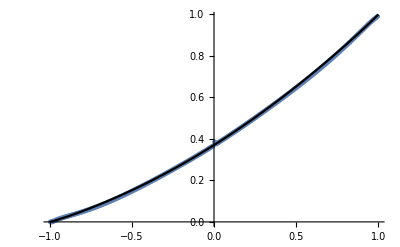

```mathematica
Show[
ListPlot[plotpoints[check[[1]],0.01,-1]],
Plot[ST`σ[u,ToExpression[roughx],ToExpression[gamma]],{u,-1,1},PlotStyle->Black]
]
```